```mathematica
MatrixForm[RandomVariate[CircularOrthogonalMatrixDistribution[3]]]
```

(0.128753-0.658303 ⅈ | -0.683296+0.130848 ⅈ | 0.249615-0.0611347 ⅈ
-0.683296+0.130848 ⅈ | -0.367143-0.606543 ⅈ | -0.0174549-0.113985 ⅈ
0.249615-0.0611347 ⅈ | -0.0174549-0.113985 ⅈ | -0.481307-0.830061 ⅈ)

```mathematica
Det[RandomVariate[CircularRealMatrixDistribution[3]]]
```

-1.

```mathematica
A=RandomVariate[CircularRealMatrixDistribution[3]]
```

{{-0.721429,0.691529,-0.0364314},{0.105624,0.16188,0.981141},{-0.684386,-0.703976,0.189827}}

```mathematica
A.Transpose[A]
```

{{1.,2.77556×10^-16,-2.37657×10^-16},{2.77556×10^-16,1.,-1.94289×10^-16},{-2.37657×10^-16,-1.94289×10^-16,1.}}

```mathematica
MatrixForm[{{1.,2.7755575615628914*^-16,-2.3765711620882257*^-16},{2.7755575615628914*^-16,1.0000000000000002,-1.942890293094024*^-16},{-2.3765711620882257*^-16,-1.942890293094024*^-16,0.9999999999999999}}]
```

(1. | 2.77556×10^-16 | -2.37657×10^-16
2.77556×10^-16 | 1. | -1.94289×10^-16
-2.37657×10^-16 | -1.94289×10^-16 | 1.)

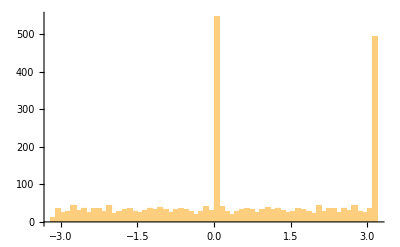

```mathematica
tiradas=1000;
matrix=ConstantArray[0,{tiradas*3}]; Dimensions[matrix];
For[i=1, i≤ tiradas, i++, a=Eigenvalues[RandomVariate[CircularRealMatrixDistribution[3]]];
matrix[[i*3]]=a[[1]];
matrix[[(i*3)-1]]=a[[2]];
matrix[[(i*3)-2]]=a[[3]];];
Histogram[Arg[matrix],60]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

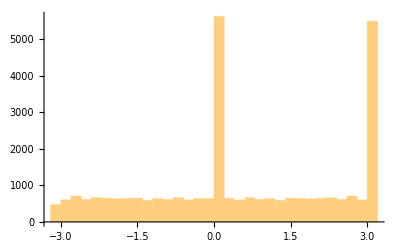

```mathematica
dim=3;
args=RandomVariate[MatrixPropertyDistribution[Arg[Eigenvalues[x]],x\[Distributed]CircularRealMatrixDistribution[dim]],10000];
eig=RandomVariate[MatrixPropertyDistribution[Eigenvalues[x],x\[Distributed]CircularRealMatrixDistribution[dim]],10000];
Histogram[Join@@args,PDF]
```

```mathematica
Mean[Arg[Flatten[eig]]]
```

0.523703

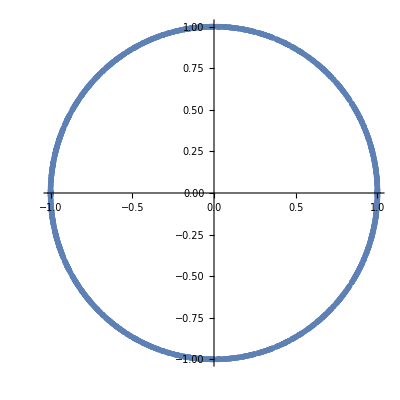

```mathematica
data=Transpose@{Re[Flatten[eig]],Im[Flatten[eig]]};
ListPlot[data, AspectRatio->1,PlotStyle->PointSize[0.01]]
```

```mathematica
###########################################################SOLO###########################################################
```

3

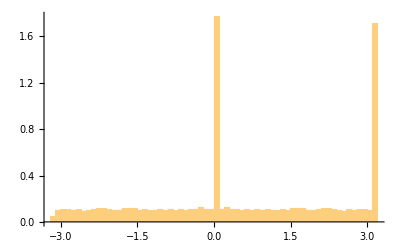

```mathematica
eig={};
tiradas=10000;
Ndim=3
For[i=1, i≤ tiradas, i++, AppendTo[eig,Arg[Eigenvalues[RandomVariate[CircularRealMatrixDistribution[Ndim]]]]]];
H1=Histogram[Join@@eig,{0.1},PDF]
```

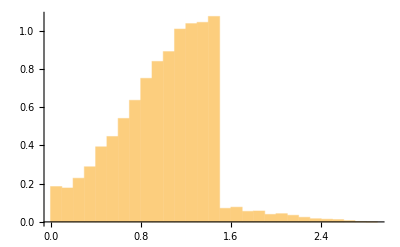

```mathematica
space={};
For[i=1, i≤ tiradas, i++,a=Sort[Arg[Eigenvalues[RandomVariate[CircularRealMatrixDistribution[Ndim]]]]];
For[j=1,j≤(Ndim-1),j++,AppendTo[space,(a[[j+1]]-a[[j]])*Ndim/(2*Pi)]  ] ];
H1=Histogram[space,{0.1},PDF]
```

```mathematica
WignerSurmisePDF[x_,β:1]:=Pi (x/2) Exp[-Pi (x/2)^2]
WignerSurmisePDF[x_,β:2]:=2 (4 x/Pi)^2 Exp[(-4/Pi) x^2]
WignerSurmisePDF[x_,β:4]:=(64/(9 Pi))^3 x^4 Exp[(-64/(9 Pi)) x^2]
P1=Plot[WignerSurmisePDF[x,1],{x,0,3}];
P2=Plot[WignerSurmisePDF[x,2],{x,0,3}];
P4=Plot[WignerSurmisePDF[x,4],{x,0,3}];
```

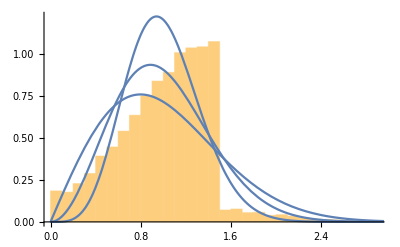

```mathematica
Show[H1,P4,P2,P1]
```

```mathematica
space={};
a=Sort[Arg[Eigenvalues[RandomVariate[CircularRealMatrixDistribution[Ndim]]]]];
AppendTo[space,(a[[2]]-a[[3]])]
```

```mathematica
###########################################################################################
```

{-2.99962}

```mathematica
AppendTo[space,9]
```

{9}

```mathematica
a
```

{-0.141973,0.141973,3.14159}

{3.14159,1.21253,-1.21253,0.466581,-0.466581,3.14159,3.14159,1.23525,-1.23525,0.,1.827,-1.827,3.14159,0.699781,-0.699781,3.1315,-3.1315,0.,0.,1.86238,-1.86238,0.,2.4641,-2.4641,1.03026,-1.03026,29948,0.34742,-0.34742,1.86114,-1.86114,0.,3.14159,0.216347,-0.216347,3.14159,0.869003,-0.869003,3.14159,0.190315,-0.190315,0.,1.91097,-1.91097,0.,2.83436,-2.83436,3.14159,0.856189,-0.856189,2.75635,-2.75635,0.}
 |  |  |  |

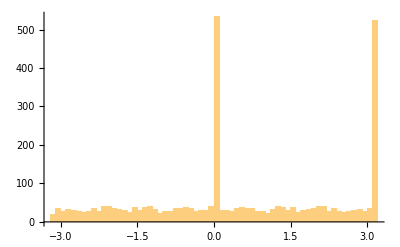

```mathematica
Flatten[args]
```

```mathematica
{-0.8842801572871732-0.466956746849397 ⅈ,-0.8842801572871732+0.466956746849397 ⅈ,1.0000000000000002+0. ⅈ,0.9114783798944732-0.4113479828380665 ⅈ,0.9114783798944732+0.4113479828380665 ⅈ,-1.+0. ⅈ,-0.9999999999999996+0. ⅈ,0.9396163837044742-0.34222953039462856 ⅈ,0.9396163837044742+0.34222953039462856 ⅈ,0.9999999999999996+0. ⅈ,-0.9641255771036553-0.2654465512575826 ⅈ,-0.9641255771036553+0.2654465512575826 ⅈ,0.6344276449048987-0.7729822529530821 ⅈ,0.6344276449048987+0.7729822529530821 ⅈ,-1.0000000000000004+0. ⅈ,-1.+0. ⅈ,0.9804925655483663-0.19655617238942932 ⅈ,0.9804925655483663+0.19655617238942932 ⅈ,-1.+0. ⅈ,0.02915445451293358-0.9995749185439046 ⅈ,0.02915445451293358+0.9995749185439046 ⅈ,0.5882346680316128-0.8086902839318265 ⅈ,0.5882346680316128+0.8086902839318265 ⅈ,-1.+0. ⅈ,1.0000000000000004+0. ⅈ,-0.7950070904165754-0.6066001369826519 ⅈ,-0.7950070904165754+0.6066001369826519 ⅈ,0.9999999999999999+0. ⅈ,-0.862436688843855-0.5061649511138117 ⅈ,-0.862436688843855+0.5061649511138117 ⅈ}
```

{-0.88428-0.466957 ⅈ,-0.88428+0.466957 ⅈ,1.+0. ⅈ,0.911478-0.411348 ⅈ,0.911478+0.411348 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.939616-0.34223 ⅈ,0.939616+0.34223 ⅈ,1.+0. ⅈ,-0.964126-0.265447 ⅈ,-0.964126+0.265447 ⅈ,0.634428-0.772982 ⅈ,0.634428+0.772982 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,0.980493-0.196556 ⅈ,0.980493+0.196556 ⅈ,-1.+0. ⅈ,0.0291545-0.999575 ⅈ,0.0291545+0.999575 ⅈ,0.588235-0.80869 ⅈ,0.588235+0.80869 ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-0.795007-0.6066 ⅈ,-0.795007+0.6066 ⅈ,1.+0. ⅈ,-0.862437-0.506165 ⅈ,-0.862437+0.506165 ⅈ}

```mathematica
dim=100;
args=RandomVariate[MatrixPropertyDistribution[Arg[Eigenvalues[x]],x\[Distributed]CircularRealMatrixDistribution[dim]],10000];
Histogram[Join@@args,{-Pi,Pi,2 Pi/40},PDF]
```

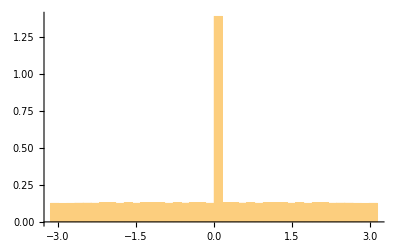

```mathematica
Histogram[Join@@args,{-Pi,Pi,2 Pi/40},PDF]
```

```mathematica
###########################################################SOLO###########################################################
```

ComplexListPlot[{-2-2 ⅈ,-1-ⅈ,0,1+ⅈ,2+2 ⅈ}]

```mathematica
a=Eigenvalues[RandomVariate[CircularRealMatrixDistribution[3]]]
```

{-0.353899+0.935283 ⅈ,-0.353899-0.935283 ⅈ,1.+0. ⅈ}

```mathematica
a[[3]]
```

1.+0. ⅈ

```mathematica
matrix[[3]]=a[[3]]
```

1.+0. ⅈ

```mathematica
matrix
```

{0,0,1.+0. ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

-0.0878606 | -0.996133
-0.996133 | 0.0878606

(-0.0878606 | -0.996133
-0.996133 | 0.0878606)

```mathematica
For[i=5,i≤7,i++,Print[i];For[j=1,j≤4,j++,Print[j]]]
```

5

1

2

3

4

6

1

2

3

4

7

1

2

3

4

```mathematica
gaps=Normalize[RandomVariate[#,10000],Mean]&/@spacingdists;
```

```mathematica
Histogram[space,{0.1},PDF]&/@gaps
```

```mathematica
Eigenvalues[RandomVariate[CircularRealMatrixDistribution[2]]]
```

{-1.,1.}